```mathematica
(*Quit[]*)
```

```mathematica
ClearAll["Global`*"];
ClearAll[Evaluate[Context[]<>"*"]];
SetDirectory@NotebookDirectory[]
```

/run/media/bryan/Resources/Documents/Base/4. 实验/6. 磁光克尔/data

```mathematica
<<"~/apps/eclipse-workspace/MathUtils/MathUtils.m"
(*<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{physics,siunitx}"}];*)
Information["Funcs`*"];
autoCollapse[];
```

```mathematica
<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{physics,siunitx}"}];

omarker=Graphics[{Thickness[.2],Disk[]}];
({colors,colorsDefault}
=colorPalette/@{"Scientific","Default"})//Grid
```

RGBColor[0.9, 0.36, 0.054] | RGBColor[0.365248, 0.427802, 0.758297] | RGBColor[0.945109, 0.593901, 0.] | RGBColor[0.645957, 0.253192, 0.685109] | RGBColor[0.285821, 0.56, 0.450773] | RGBColor[0.7, 0.336, 0.] | RGBColor[0.491486, 0.345109, 0.8] | RGBColor[0.71788, 0.568653, 0.] | RGBColor[0.70743, 0.224, 0.542415] | RGBColor[0.287228, 0.490217, 0.664674] | RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636] | RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922] | RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023] | RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854] | RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]
RGBColor[0.368417, 0.506779, 0.709798] | RGBColor[0.880722, 0.611041, 0.142051] | RGBColor[0.560181, 0.691569, 0.194885] | RGBColor[0.922526, 0.385626, 0.209179] | RGBColor[0.528488, 0.470624, 0.701351] | RGBColor[0.772079, 0.431554, 0.102387] | RGBColor[0.363898, 0.618501, 0.782349] | RGBColor[1, 0.75, 0] | RGBColor[0.647624, 0.37816, 0.614037] | RGBColor[0.571589, 0.586483, 0.] | RGBColor[0.915, 0.3325, 0.2125] | RGBColor[0.40082222609352647, 0.5220066643438841, 0.85] | RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142] | RGBColor[0.736782672705901, 0.358, 0.5030266573755369] | RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]

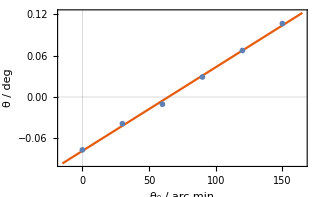

plots/calibrationPlot.pdf

```mathematica
calData=FromCharacterCode[
BinaryReadList["cal.dat"],"MacintoshChineseSimplified"
]//StringDelete["\r"]//StringSplit[#,"\n"]&\
//Select[StringStartsQ[" "]]//StringRiffle[#,"\n"]&//ImportString;

calibrationPlot=Show[
Plot[
Evaluate[
LinearModelFit[calData,xx,xx]
][x]
,Evaluate@{x,Sequence@@MinMax[calData⟦All,1⟧,Scaled[.1]]}
,PlotTheme->"Scientific"
,PlotRange->All
,FrameLabel->Block[{θ},{
Row[{Subscript[θ, 0]," / arc min"}]
,Row[{θ," / deg"}]
}]
,ImageSize->320
]
,ListPlot[
calData
]
]
exportPlot[calibrationPlot]
```

```mathematica
angleLst={2.5,2,1,0,-1,3};
datLst=FromCharacterCode[
BinaryReadList["All.dat"],"MacintoshChineseSimplified"
]//StringDelete["\r"]//StringSplit[#,"\n\n"]&//Select[StringContainsQ["克尔转角"]];

dataset=(
#//StringSplit[#,"\n"]&//Select[StringStartsQ[" "]]//StringRiffle[#,"\n"]&//ImportString
)&/@datLst;

"Rearrage by input angle of polarization";
dataset=dataset⟦Ordering[angleLst]⟧;
"NOTE: Sequence matter! Sort dataset first, then angles";
angleLst=angleLst⟦Ordering[angleLst]⟧;

ListLinePlot[#1⟦All,{1,3}⟧,PlotLabel->#2,PlotRange->All]&@@@Transpose[{
dataset,angleLst
}]//Partition[#,3]&//GraphicsGrid;

"Phase correction";
dataset⟦4;;,All,{2,3}⟧*=-1;
```

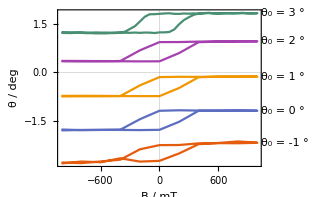

plots/hysteresisCurves.pdf

```mathematica
hysteresisCurves=ListLinePlot[
Evaluate[
dataset⟦
#
,All,{1,3}⟧
]
,PlotTheme->"Scientific"
,ImageSize->320
,PlotLabels->Block[{θ},Placed[
Row[{
Subscript[θ, 0]," = ",#," ","°"
}]&/@angleLst⟦#⟧
,After]]
,FrameLabel->Block[{B,θ},{
Row[{B," / mT"}]
,Row[{θ," / deg"}]
}]
,PlotRangePadding->{Automatic,Scaled[.05]}
]&[
Position[angleLst,_?(#≠2.5&)]//Flatten[#,1]&
]

exportPlot[hysteresisCurves]
```

```mathematica
sampleData=
(
#//StringSplit[#,"\n"]&//Select[StringStartsQ[" "]]//StringRiffle[#,"\n"]&//ImportString
)&/@(
FromCharacterCode[
BinaryReadList["2.5.dat"],"MacintoshChineseSimplified"
]//StringDelete["\r"]//StringSplit[#,"\n\n"]&//Select[StringContainsQ["克尔椭率"]]
)//First;
```

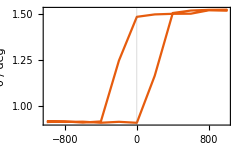
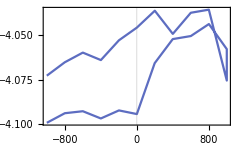

{plots/sampleTheta.pdf,plots/sampleEpsilon.pdf}

```mathematica
{sampleTheta,sampleEpsilon}=ListLinePlot[#1
,PlotTheme->"Scientific"
,ImageSize->240
,FrameLabel->{
Block[{B},Row[{B," / mT"}]]
,#2
}
,PlotStyle->#3
]&@@@{
{dataset⟦First[FirstPosition[angleLst,2.5]],All,{1,3}⟧,Row[{HoldForm[θ]," / deg"}],colors⟦1⟧}
,{sampleData⟦All,{1,3}⟧,HoldForm[ϵ],colors⟦2⟧}
};
{sampleTheta,sampleEpsilon}//Magnify[#,1.2]&

exportPlot/@holdItems[{sampleTheta,sampleEpsilon}]
```

```mathematica
detailedData=dataset⟦
Sequence@@(
Position[angleLst,_?(#==3&)]//Flatten[#,1]&
)
,All,{1,3}⟧;
```

```mathematica
thetaZero=detailedData//Select[Abs[#⟦1⟧]>500&]//Mean//Last
```

1.51806

```mathematica
shiftedData={#1,#2-thetaZero}&@@@detailedData;
shiftedData//Select[Abs[#⟦1⟧]>500&]//Transpose//Last//Abs//Mean
```

0.300557

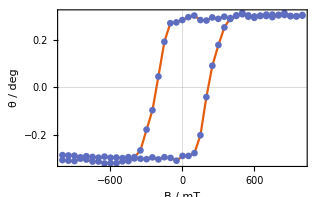

plots/hysteresisDetails.pdf

```mathematica
hysteresisDetails=Show[
ListLinePlot[
#
,PlotTheme->"Scientific"
,PlotStyle->colors⟦1⟧
,ImageSize->320
,FrameLabel->Block[{B,θ},{
Row[{B," / mT"}]
,Row[{θ," / deg"}]
}]
,PlotRangePadding->{Automatic,Scaled[.05]}
]
,ListPlot[
#
,PlotStyle->Directive[
colors⟦2⟧
,PointSize[.015]
]
]
]&@Evaluate[
shiftedData
]

exportPlot[hysteresisDetails]
```

```mathematica
Interpolation/@(
Partition[#,Round[Length[#]/2]]&@shiftedData
)
Block[{x},
zeros=x/.FindRoot[#[x],{x,0}]&/@%;
zeros//Print;
zeros//Mean//Print;
mean=Mean[Abs[zeros]];
mean//Print;
MinMax[zeros]-{-1,1}*mean
]
```

{InterpolatingFunction[…],InterpolatingFunction[…]}

{213.676,-214.965}

-0.644343

214.321

{-0.644343,-0.644343}